```mathematica
(* This Notebook defines modules to find ϕ[n], ϵ[n], η[n], and ns[n]. It does not use the slow roll approx and instead integrates the Klein Gordon equation to find ϕ[n]. It then plots where monomial potentials fall on the r-ns plane. *)
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
(* Define a potential *)
(*v[x_] := x^4*(1-Log[x])*)
v[x_] := x^4
vp[x_]=v'[x]
(* Define a module to find ϕ60 *)
findϕ60 := Module[{ϕ0},
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
Print["ϕ0 = ",ϕ0];
f[t_] = Integrate[v[x]/v'[x],{x,ϕ0,t}];
ϕ60 = t/.Last[NSolve[60==f[t],t]];
Return[ϕ60]] 
ϕ60 = findϕ60
Print["ϕ60 = ",ϕ60]
```

4 x^3

ϕ0 = 2.82843

22.0907

ϕ60 = 22.0907

ϕ0 = 2.82843

{{ϕ→InterpolatingFunction[{{0., 60.}}, <>]}}

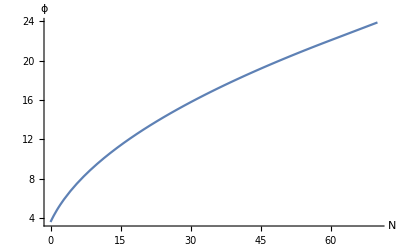

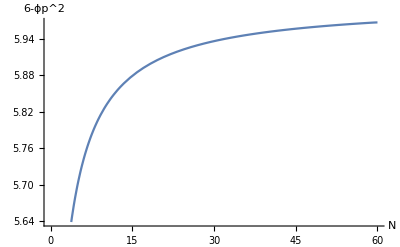

```mathematica
(* Define a module to find ϕ[n] *)
findϕ := Module[{h,hsq,nsr,ϕ60,ϕp60},
(* Define H as a function of number of efolds *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
(* (* Define number of efolds using slow-roll approx *)
nsr[x_] := v[x]/v'[x];(* Strictly speaking, I get the differential form dN=v[x]/v'[x] dx *)
(* find ϕ60, ϕ at n=60 *)
ϕ60 = Evaluate[Last[FindRoot[{nsr[x]-60==0},{x,1}]]]; *)
ϕ60 = findϕ60;
(* find ϕp60 = ϕ'[60] *)
ϕp60 = vp[ϕ60]/v[ϕ60] ;
(* Solve for ϕ[n] *)
(* Note that this form of the differential equation only holds provided: 6-(ϕ'[n])^2≠0. *)NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*v'[ϕ[n]]==0,ϕ[60]==ϕ60,ϕ'[60]==ϕp60},ϕ,{n,60,0},InterpolationOrder->All]]
ϕsol = findϕ
Plot[Evaluate[ϕ[n]/.ϕsol],{n,70,0},AxesLabel->{N,ϕ}]
Plot[Evaluate[6-(ϕ'[n])^2/.ϕsol],{n,60,0},AxesLabel->{N,"6-ϕp^2"}]
```

```mathematica
(* Define a module to find ϕ[n] integrating from ϕ0 instead of ϕ60 *)
findϕUsingϕ0 := Module[{h,hsq,nsr,ϕ0,ϕp0},
(* Define H as a function of number of efolds 
Input: v[ϕ[n]], vp[ϕ[n]]
Output: ϕsol[n] *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
(* find ϕp0 = ϕ'[0] *)
ϕp0 = vp[ϕ0]/v[ϕ0] ;
(* Solve for ϕ[n] *)
(* Note that this form of the differential equation only holds provided: 6-(ϕ'[n])^2≠0. *)NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*v'[ϕ[n]]==0,ϕ[0]==ϕ0,ϕ'[0]==ϕp0},ϕ,{n,0,70},InterpolationOrder->All]]
ϕsol = findϕ
Plot[Evaluate[ϕ[n]/.ϕsol],{n,70,0},AxesLabel->{N,ϕ}]
Plot[Evaluate[6-(ϕ'[n])^2/.ϕsol],{n,60,0},AxesLabel->{N,"6-ϕp^2"}]
```

ϕ0 = 2.82843

{{ϕ→InterpolatingFunction[{{0., 60.}}, <>]}}

-Graphics-

-Graphics-

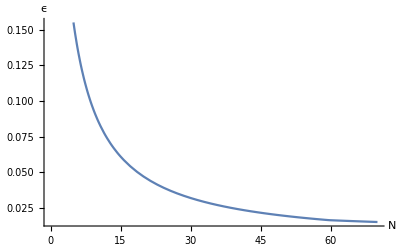

{0.572735}

```mathematica
findϵ := Module[{ϵ},
(* Find ϵ[n] 
Input: v[ϕ[n]], ϕsol 
Output: ϵ[n] *)
ϵ[n_] := 1/2*D[Log[v[ϕ[n]/.ϕsol]],n];
Return[ϵ[n]]]
ϵ[n_] := findϵ 
Plot[Evaluate[ϵ[n]],{n,70,0},AxesLabel->{N,ϵ}]
ϵ[n]/.{n->0}
```

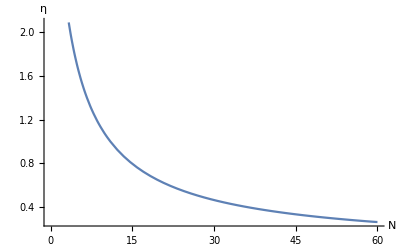

```mathematica
findη := Module[{ϕp,η},
(* Find η[n] 
Input: v[x], vp[ϕ[n]], ϕsol
Output: η[n] *)
ϕp[x_] := v'[x]/v[x];
η[n_] := 1/2*D[Log[vp[ϕ[n]/.ϕsol]]^2,n];
Return[η[n]]]
η[n_] := findη
Plot[Evaluate[η[n]],{n,60,0},AxesLabel->{N,η}]
```

ns[60] = {0.959016}

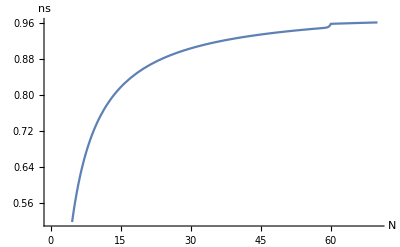

```mathematica
findNs := Module[{ns,ϕ60},
(* Find ns[n]
Input: ϵ[n],
Output: ns[n] *)
ns[n_] := 1-2*ϵ[n]+D[Log[ϵ[n]],n];
Return[ns[n]]]
ns[n_] := findNs
Print["ns[60] = ",ns[n]/.{n->60}]
Plot[Evaluate[ns[n]],{n,70,0},AxesLabel->{N,ns}]
```

{}

ϕ0 = 1.41421

p = 2     ϵ[0] = 0.39571     ns[60] = 0.975207

ϕ0 = 2.12132

p = 3     ϵ[0] = 0.498494     ns[60] = 0.967078

ϕ0 = 2.82843

p = 4     ϵ[0] = 0.572735     ns[60] = 0.959016

ϕ0 = 3.53553

p = 5     ϵ[0] = 0.628799     ns[60] = 0.95102

ϕ0 = 4.24264

p = 6     ϵ[0] = 0.672567     ns[60] = 0.943089

ϕ0 = 4.94975

p = 7     ϵ[0] = 0.707656     ns[60] = 0.935223

ϕ0 = 5.65685

p = 8     ϵ[0] = 0.736373     ns[60] = 0.927419

ϕ0 = 6.36396

p = 9     ϵ[0] = 0.760296     ns[60] = 0.919679

ϕ0 = 7.07107

p = 10     ϵ[0] = 0.780513     ns[60] = 0.912

ϕ0 = 7.77817

p = 11     ϵ[0] = 0.797811     ns[60] = 0.904382

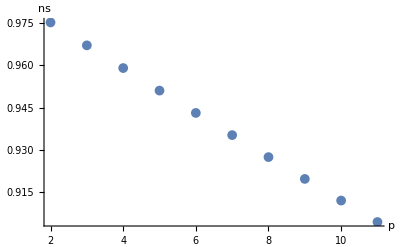

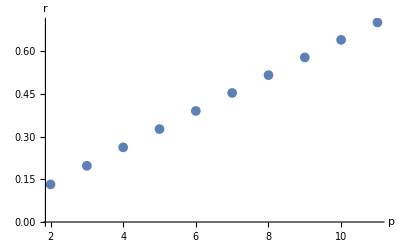

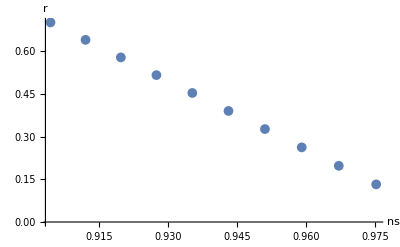

```mathematica
nsList = {}; rList = {};pList = {}
For[p=2,p<12,p++,
Clear[v,ϕsol,ns,ϵ];
v[ϕ_] := ϕ^p;
vp[x_]=v'[x];
ϕsol = findϕ;
ϵ[n_] = Last[findϵ ];
ns[n_] = findNs;
Print["p = ",p,"     ϵ[0] = ",ϵ[n]/.{n->0},"     ns[60] = ",ns[n]/.{n->60}];
AppendTo[nsList,ns[n]/.{n->60}];
AppendTo[rList,16*(ϵ[n]/.{n->60})];
AppendTo[pList,p]]
ListPlot[Thread[{pList,nsList}],AxesLabel->{"p",ns},PlotMarkers->{●,10}]
ListPlot[Thread[{pList,rList}],AxesLabel->{"p",r},PlotMarkers->{●,10}]
ListPlot[Thread[{nsList,rList}],AxesLabel->{ns,r},PlotMarkers->{●,10}]
```

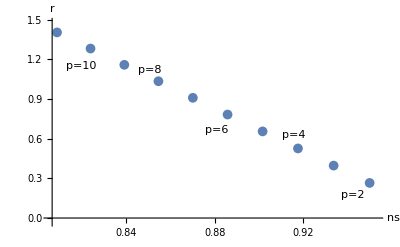

-Graphics-

```mathematica
(* Find the degrees of fine-tuning: Zϵ and Zη *)
findZϵ := Module[{roots},
(* Find Zϵ 
Input: ϵ[n], 
Output: Zϵ *)
roots = FindRoot[ϵ[n],{n,30}]; 
roots = Normal[Select[Association[roots],#>0&#<60&]];
(* roots = Solve[ϵ[n]==0,n,{n,0,60}]; *)
Print["Roots = ",roots];
Return[Length[roots]]
]
Zϵ = findZϵ
```

InterpolatingFunction::dmval: Input value {63.1984} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {191.897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Roots = {}

0